# Unfolding

## Definitions and packages (you shall manually execute this section)

Change this line to load the package QMB in https://github.com/deleonja/libs from wherever it is in your machine (make sure you have the up to date version of the package):

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\SFF

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\MG files\\SFF\\QMB.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
?Unfold
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

## Ising chain

Consider the eigenergies of the odd symmetric subspace of the Ising Hamiltonian with transverse and longitudinal fields

for a set of parameters in which the system is chaotic (h_x=1, h_z=0.48, J=1.12):

## Diagonalization

```mathematica
J=1;
g=1;
h=0.1;
```

```mathematica
L=14;
```

```mathematica
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
```

```mathematica
eveneigenval=Quiet[Eigenvalues[system[[1]]]];
```

```mathematica
oddeigenval=Quiet[Eigenvalues[system[[2]]]];
```

## Unfolding

```mathematica
energies=oddeigenval;
```

```mathematica
energies=eveneigenval;
```

The density of states (DOS) is well approximated by a Gaussian distribution:

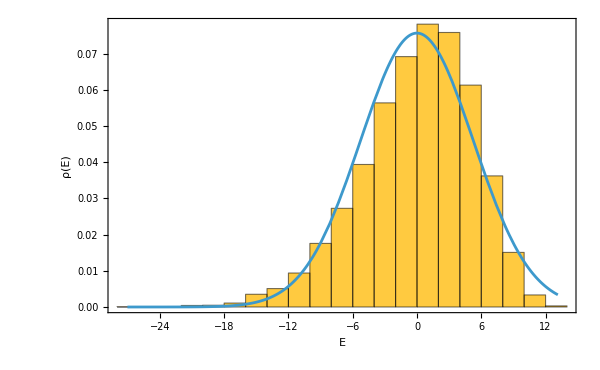

```mathematica
skd=SmoothKernelDistribution[energies];
{μ,σ}={Moment[skd,1],√(Moment[skd,2]-Moment[skd,1]^2)};
Show[
Histogram[energies,Automatic,"PDF",
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"E","ρ(E)"},
ImageSize->600],
Plot[PDF[NormalDistribution[μ,σ],x],{x,Min[energies],Max[energies]}]
]
```

```mathematica
(*Unfold the WHOLE spectrum*)
{unfoldedEnergies,smoothCDF}={#["UnfoldedLevels"],#["SmoothCDF"]}&@Unfold[Sort[energies]];
```

Verify the unfolding worked by checking the mean level spacing is approximately 1:

```mathematica
Mean[Differences[unfoldedEnergies]]
```

1.00012

Compare the staircase function with the smoothed version used to unfold the spectrum:

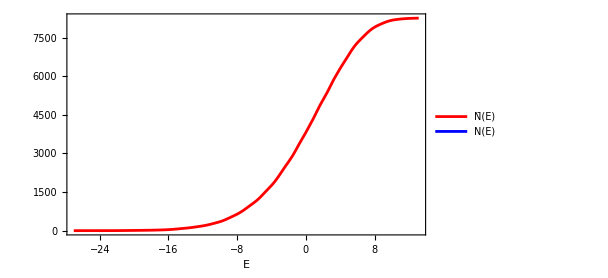

```mathematica
Plot[{smoothCDF[x],Length[energies]*CDF[energies,x]},{x,Min[energies],Max[energies]},
PlotStyle->{Red,Blue},
PlotLegends->Placed[LineLegend[{"N̄(E)","N(E)"},LabelStyle->Directive[FontSize->20]],{Left,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->22],
FrameLabel->{"E",""},
ImageSize->450
]
```

After unfolding, the density of states has become almost flat (as should be):

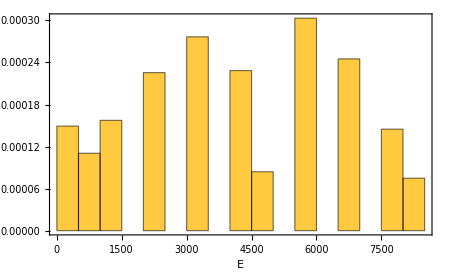

{{0.,500.,1000.,1500.,2000.,2500.,3000.,3500.,4000.,4500.,5000.,5500.,6000.,6500.,7000.,7500.,8000.,8500.},{0.000149225,0.000110465,0.000157461,0.,0.000225533,0.,0.000276647,0.,0.00022844,0.0000840601,0.,0.000303295,0.,0.000245155,0.,0.000144864,0.0000748547}}

```mathematica
Histogram[unfoldedEnergies,Automatic,"PDF",
Frame->True,
FrameStyle->Directive[Black,FontSize->15],
FrameLabel->{"E",""},
ImageSize->450
]
N[HistogramList[unfoldedEnergies,Automatic,"PDF"]]
```

We compute the level spacing distribution P(s) of the unfolded spectrum only within the bulk (where the ρ(E) of unfolded energies is constant):

```mathematica
unfoldedEnergies//Dimensions
```

{8256}

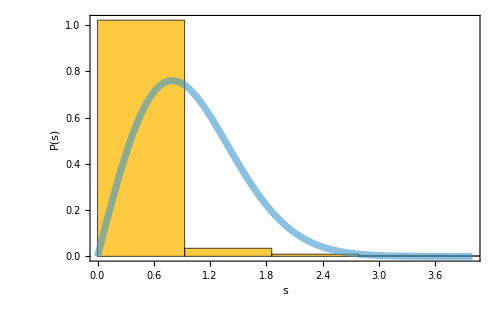

```mathematica
Show[
Histogram[Differences[unfoldedEnergies[[500;;7500]]],Automatic,"PDF",
PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"s","P(s)"},
ImageSize->500
],
(*wigner surmise*)
Plot[PDF[RayleighDistribution[√(2/π)],s],{s,0,4},PlotStyle->Directive[Thickness[0.01],Opacity[0.6]]]
]
```

```mathematica
MeanLevelSpacingRatio[Sort[eveneigenval]]
```

0.42428

```mathematica
MeanLevelSpacingRatio[Sort[oddeigenval]]
```

0.406347

```mathematica
numberVariance[energies_List,lmax_]:=Module[{e=Sort[energies],lvals,sigma2},lvals=Range[1,lmax];
sigma2=ParallelTable[Mean[Table[With[{e0=e[[i]],count=Count[e,_?(e0<=#<=e0+l&)]},(count-l)^2],{i,1,Length[e]-l}]],{l,lvals},DistributedContexts->Full];
Transpose[{lvals,sigma2}]]
```

```mathematica
data=numberVariance[unfoldedEnergies,30];
```

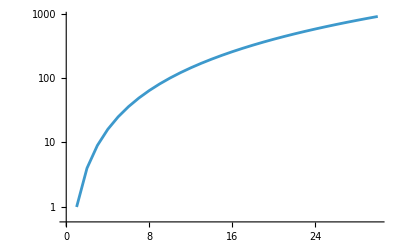

```mathematica
dataplot=ListLogPlot[data,FrameLabel->{"L","σ^2(L)"},Joined->True]
```

```mathematica
theory=Plot[{x,Log[2Pi*x]/Pi^2},{x,1,30},FrameLabel->{"L","σ^2(L)"},PlotStyle->Directive[Black,Dashed]];
```

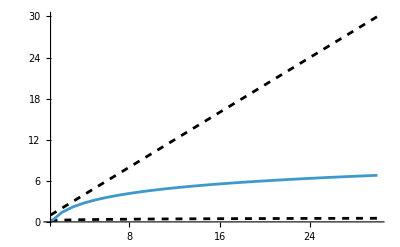

```mathematica
Show[{theory,dataplot}]
```